```mathematica
Task 3 Experiment Set 1
```

```mathematica
Exp1 = {4.61*10^-1, 2.42*10^-1,1.30*10^-1,6.62*10^-2, 3.97*10^-2,6.26*10^-2}
```

{0.461,0.242,0.13,0.0662,0.0397,0.0626}

```mathematica
Q = {2,4,8,16,32,64}
```

{2,4,8,16,32,64}

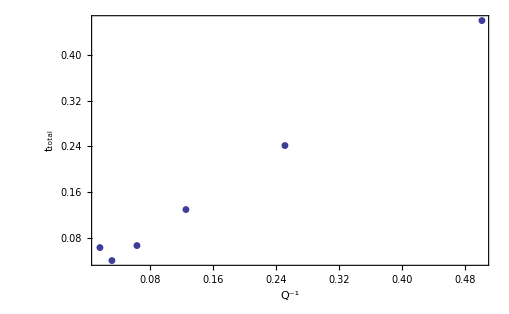

```mathematica
plotframedGT = {{Style[
     "t_total"(*,Italic*), 
     17],}, {Style["Q^-1"(*,Italic*), 17],}};
ListPlot[Table[{1/Q⟦i⟧,Exp1⟦i⟧},{i,0,Length[Q]}],
PlotRange-> All,Frame->{{True,True},{True,True}},FrameLabel->plotframedGT,AspectRatio->1/GoldenRatio,AxesStyle->{White,Dashed},FrameTicksStyle->16,PlotMarkers->{Automatic(*,Medium*)}]
```